# Mathematica - A Fantastic Playground

## Before we Begin

#### Explore: Dynamic Functionality

Start exploring this notebook on your own. All you need is a mouse! Play around with the sliders and other controllers below and see what happens

```mathematica
(* Pottery *)
DynamicModule[{dd=3Pi/2,f,pts={{0,2},{1,2},{3,3},{5,2},{6,2},{7,3},{9,3}}},
f=Interpolation[pts,InterpolationOrder->2,Method->"Spline"];
Grid[{
{LocatorPane[Dynamic[pts,(f=Interpolation[#,InterpolationOrder->2,Method->"Spline"];pts=#)&],Dynamic[Plot[f[t],{t,0,9},PlotRange->{{0,9},{0,4}}]]],
Slider[Dynamic[dd],{.1,2Pi}]},
{Dynamic[RevolutionPlot3D[{f[t]},{t,0,9},{d,0,dd},Mesh->None,PlotStyle->Directive[Orange,Specularity[White,10]],RevolutionAxis->{1,0,0},PlotRange->{All,{-4,4},{-4,4}},ImageSize->300],TrackedSymbols:>{f,dd}],SpanFromLeft}
}]
]
```

```mathematica
(* Rotating about a point *)
Manipulate[Graphics[{Gray,Rectangle[],Black,Rotate[Rectangle[],θ,center],Red,PointSize[0.03],Point[center]}, PlotRange->2, Axes->True],
"The rotation variable runs from 0 to 2π:",
{θ,0,2π, ControlType -> Animator, ImageSize -> Small},
Delimiter,
"Rotation happens around whatever center the user specifies",
{{center,{0,0}},{0,0},{1,1}, ControlType -> Slider2D},
ControlPlacement -> Left
]
```

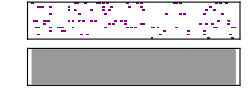

```mathematica
(* Random music *)
Sound[Table[SoundNote[NestList[#+4&,-24,n=10](RandomChoice[{1-#,#}->{0,1}]&/@(RealDigits[N[1/7,n+1]][[1]]/50))/.x_/;x==0->None,0.25],{102}]]
```

```mathematica
(* Pretty graphic *)
Manipulate[Graphics[Polygon[Table[r^n{-Sin[n*a],Cos[n*a]},{n,0,L}]],PlotRange->P],
{P,1,0},{{r,.98},1,.95},{{a,2.6},0,2Pi}, {{L,300},1,1000,1}]
```

```mathematica
(* Bouncing balls *)
Framed@DynamicModule[{contents={}},EventHandler[Graphics[{Text[Style["Click on me!",18],{0.5,0.8}],PointSize[0.1],Point[Dynamic[contents=Map[If[#[[1,2]]≥0,{#[[1]]-#[[2]],#[[2]]+{0,0.001}},{{#[[1,1]],0},{1,-(0.8+RandomReal[{0,0.2}])}#[[2]]}]&,contents];Map[First,contents]]]},PlotRange->{{0,1},{0,1}}],"MouseDown":>(AppendTo[contents,{MousePosition["Graphics"],{0,0}}])]]
```

How much code do you think each of these requires? To ungroup (or open) a cell, double mouse click on the down arrow at the very right of the screen.

## Beginner Section: A Gentle Introduction

Important sections are marked with (!!!)

#### Overview

11:00-12:00pm 	A Gentle Introduction Mathematica from the Ground Up
12:00-12:30pm 	Lunch Yummy
12:30-1:30pm 	No-holds-barred The Mathematica Power User

### Basics

#### Calculator

You can use Mathematica as a (super-awesome) calculator

Evaluate cells using Shift + Enter

```mathematica
1+1
```

```mathematica
(-2)*(-2)
```

#### The Rules

The rules for the Mathematica language are:

Most built-in commands begin with a capital letter and are non-abbreviated, standard English words. If a command consists of several words, the first letter of each word is capitalized. The complete word is written without spaces. Ex: , , ...

Main Exceptions: Mathematical shorthand notations (, , , , )

Symbols defined by the user usually begin with lowercase letters. Variable names can be arbitrarily long and can include

Uppercase letters

Lowercase letters

Numbers (although numbers cannot be used as the first character)

#### Explore: Ridiculously Complex Arithmetic

Note: To create code, place the cursor between two cells and start typing

Evaluate 15/48+19/400+16/25

What is the last digit of 2^1000

#### Basic Keyboard Shortcuts

Mouse wheel - Scroll up and down in the notebook

←/→: Move left/right one character
↑/↓: Move up/down in the notebook

Enter - New line (inside of a cell, this stays within the cell)
Shift + Enter: Evaluate cell
NumPad Enter: Evaluate cell

Control + c: Copy
Control + v: Paste

Control + z: Undo
Control + y: Redo (i.e. undo an undo)

#### Intermediate Section: Multiple Forms of an Expression

There are many ways to compute the square root of x. You can raise x to the 1/2 power; you can using the shortcut Control+2 to create a square root symbol (√) and then put x underneath it; you can use the  command. All of these are equivalent, so choose whichever you like. If you want to find out how to create a symbol, such as the √ symbol you can always look at the documentation page of its corresponding command (it will be in the Details section of the  page).

```mathematica
4^(1/2)
Sqrt[4]
√4
```

#### (!!!) Brackets

Assign values to a variable using =

```mathematica
var=5
```

```mathematica
var-3
2*var
```

The three types of parenthesis play different roles

Braces {} are used to enclose components of vectors and elements of sets (any number of elements of arbitrary type are allowed, which can be nested to any level)

Ex: Create a list with the elements 1, 5, 25, 125, 625, 3125, 15625, and 78125

```mathematica
{1,5,25,125,625,3125,15625,78125}
```

Brackets [] are used for enclosing arguments in functions

Ex: Apply the function Exp (the exponential function) of the arguments 5, 0, and x. These yield the values ⅇ^5, ⅇ^0=1, and ⅇ^x, respectively

```mathematica
Exp[5]
Exp[0]
Exp[z]
```

Parentheses () are used exclusively for grouping

Ex: Normal order of operations would evaluate 2*3+4 as (2*3)+4=10. If we instead want to evaluate 2*(3+4)=14 we must add parentheses

```mathematica
2*3+4
2*(3+4)
```

#### Explore: Total

The function  sums up the elements of a list. Define list as a list containing 2, 6, 12, 20, 30 and then use  (with hard brackets) on this list. Compare the result to 2+6+12+20+30

#### Intermediate Section: Output of Set

When you give a variable a value, you always see the output of that variable’s value. For example, define list to be a list containing 1, 2, 3, 4, and 5

```mathematica
list={1,2,3,4,5}
```

The output is the expected list containing 1, 2, 3, 4, and 5. Suppose we instead defined list as

```mathematica
list={1*2,2*3,3*4,4*5,5*6}
```

The computations have been evaluated prior to assigning these values to list. In other words, the first element in list equals 2 and not 1*2

```mathematica
list[[1]]
```

#### Intermediate Section: More Syntax

More useful Mathematica syntax includes:

Prevent the display of (long) results by using a semicolon at the end of input: expression;

Independent inputs can either be placed on separate lines or they can be separated by semicolons: inputStatement_1; inputStatement_2; …; inputStatement_n

The last expression given by Mathematica: %

The next-to-last (penultimate) expression given by Mathematica: %%

The i^th output of Mathematica: %i or Out[i]

When an expression is too long to fit on one line, the symbol \ (or ) is displayed, indicating that the expression is continued on the next line (if an expression is incomplete when the end of the line is reached, the expression is automatically considered to be continued on the next line)

Comments can be written in the form, (* material to be ignored when sent to the Mathematica kernel *) (comments can be inserted anywhere in Mathematica source code)

Information on the command command: ?command

"Ordinary", Greek, Gothic, Script, and double-struck letters represent different letters (B≠Β≠𝔅≠ℬ≠𝔹), and symbol names made from them are considered different. But plain, bold, italic, bold-italic, and underlined versions of a letter are considered equal (B=B=B=B=B)

#### (!!!) Documentation Center

Your best resource for:

Learning the functionality of a function (i.e. what can  do?)

Searching for new functions (Ex: if you want the mean of a list of quantities, search for mean)

Tutorials on all aspects of Mathematica (Ex: , , , , , ...)

Shortcuts:

F1 (Windows), Fnct + F1 (Mac): Open the Documentation Center

Mouse click a link: Navigate to that link

Shift+Click a link: Open up a new Documentation Center at that link

Shift+F1: Open a new Documentation Center main page

#### Explore: Factorial, Table, Mean

What is the first digit of 10000 factorial (i.e. 10000*9999*9998*···*1)

The  function is useful for constructing lists. Create a list of the first 100 prime numbers (Hint: Use the function  inside of )

```mathematica
(* First 4 usages of Table from the Documentation Center *)
Table[5,{10}]
Table[5*i,{i,10}]
Table[5*i,{i,0,10}]
Table[5*i,{i,0,10,2}]
```

What is the mean of the first 100 prime numbers?

```mathematica
Mean[Table[Prime[j],{j,1,100}]]
```

#### Symbolics

```mathematica
a+b
a*b
a^b
```

Polynomial in x can be ed or ed

```mathematica
poly=(-2+x)(-2-x-3 x^2+2 x^3)
```

```mathematica
Expand[poly]
Factor[poly]
```

Note the blue x and black poly

```mathematica
(z+1)^2
```

```mathematica
y=1;
(y+1)^2
```

#### Clearing Values

If x had previously been set

```mathematica
x=1;
x^2+1
```

We can  its definition

```mathematica
Clear[x]
```

x is now blue (not black), indicating that it is now a symbol. You can clear multiple variables at the same time

```mathematica
x=1
y=2
z=3
```

```mathematica
Clear[x,y,z]
```

### Intermediate Section: Dive Deeper

#### Polynomial Ordering

(In case you are curious about the ordering Mathematica uses to display polynomials)

#### Giving Symbols Values

Suppose you are given a polynomial poly that you want to evaluate at various values of x.

```mathematica
poly=4+5 x^2-7 x^3+2 x^4
```

For example, you want to know what poly equals at x=2 and x=5. You can do so by using  which has a convenient shorthand notation (/.)

```mathematica
poly/.x->2
poly/.x->5
(* Equivalent form *)
ReplaceAll[poly,x->2]
ReplaceAll[poly,x->5]
```

applies to every instance of the replacement expression. For example,

```mathematica
{{x,y,{x,x},z,{{{x}}}}}/.x->1
```

As an advanced example, you can take the underlying structure of an object such as a graph

```mathematica
ParametricPlot3D[{Sin[u],Cos[u],u/5},{u,0,4π}]
```

and alter the way that it appears. As two examples, we change the underlying mechanism used in the plot from Line into Tube, giving the plot a more 3D appearance.

```mathematica
ParametricPlot3D[{Sin[u],Cos[u],u/5},{u,0,4π}]/.Line->Tube
```

#### Vectors, Matrices, Tensors

Lists are very generic objects. We can represent vectors (Ex: {a,b,c}), matrices (Ex: {{a,b},{c,d}}), or . These have the usual  such as matrix multiplication, cross products, etc.

```mathematica
(* Matrix multiplication *)
{{a,b},{c,d}}.{{e,f},{g,h}}
(* Cross products *)
Cross[{a,b,c},{d,e,f}]
```

Lists can also be ragged, meaning that they do not need to have the same number of elements at each level (Ex: {{a,b,c,d,e},{f}}). This generality makes them extremely powerful.

Construct a list of the first 10 integers in the form {j,divisors of j}.

```mathematica
Table[{j,Divisors[j]},{j,1,10}]
```

### (!!!) Numerics

#### Overview

Exact input will yield exact output

```mathematica
Sin[Pi/3]
```

Entering non-exact (i.e. numerical) input yields numerical output

You can also use  to force numerical answers

```mathematica
(* Entering non-exact input *)
Sin[Pi/3.]
1.*Sin[Pi/3]
(* Using N on an exact number *)
N[Sin[Pi/3]]
```

Arbitrary precision is supported on exact values

```mathematica
N[Sin[Pi/3],1000]
```

#### Explore: Powers of 5

Consider 1/5^k where k is a positive integer. What is the smallest value of k such that 1/5^k<10^-7?

### Visualization

Plotting a function of one variable is done using

```mathematica
Plot[Sin[x],{x,0,6Pi}]
```

Plot has lots of options, enabling you to customize nearly the axes, ticks, legend, color... You can also plot multiple functions very easily.

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},AxesLabel->{"x"},PlotLabel->"Really Cool Plot"]
```

### (!!!) Application: Simplifying Expressions

#### Simplify

is one of the most incredible functions that Mathematica has to offer.  will accomplish in a split second what can take you hours to do by hand.

```mathematica
Simplify[(-1024+5120 x-11520 x^2+15360 x^3-12416 x^4+2944 x^5+8160 x^6-14400 x^7+13260 x^8-8044 x^9+3359 x^10-960 x^11+180 x^12-20 x^13+x^14)/(-2+x-2 x^2+x^3)]
```

Most expressions are not simplified automatically, but  does the trick

```mathematica
(* We know that this answer must be 1/(x^3+1) *)
result=D[Integrate[1/(x^3+1),x],x]
```

```mathematica
(* Mathematica can simplify the above result to find this simpler form *)
Simplify[result]
```

#### FullSimplify

is ’s big brother!

always returns an answer at least as simple as , but it may take more time. However, it has more algorithms at its disposal

```mathematica
Simplify[Gamma[x] Gamma[1 - x]]
FullSimplify[Gamma[x] Gamma[1 - x]]
```

#### Explore: Binomial (Coefficients)

Use  to prove get nice formula for Binomial[n+1,k+1]/Binomial[n,k]=(n+1
k+1)/(n
k)

### (!!!) Application: Solving Equations

#### Exact Solving

solves a system of equations

When entering equations in the form lhs==rhs you must use == (which indicates equality) instead of = (which indicates defining the variable lhs to have the value rhs)

```mathematica
(* Solve a linear equation *)
Solve[5x+2==7/2,x]
```

```mathematica
(* Solve finds all solutions, real or complex *)
Solve[x^4==1,x]
```

```mathematica
(* Solve for multiple variables *)
Solve[{x*y==35,x+y==12},{x,y}]
```

```mathematica
(* Solve where the unit circle intersects the line passing through (-2,1) and (1,-2) *)
Subscript[ℛ, 1]=Circle[];
Subscript[ℛ, 2]=Line[{{-2,1},{1,-2}}];
solve=Solve[{x,y}∈Subscript[ℛ, 1]&&{x,y}∈Subscript[ℛ, 2],{x,y}];
Graphics[{{Subscript[ℛ, 1],Purple,Subscript[ℛ, 2]},{Red,PointSize[0.015],Point[{x,y}]/.solve}}]
```

#### Numerical Solving

is a numerical version of

```mathematica
(* Find exact solutions to a system of equations *)
Solve[{x^2+y^2==1,x+y^2==2},{x,y}]
(* Find approximate solutions to a system of equations *)
NSolve[{x^2+y^2==1,x+y^2==2},{x,y}]
```

#### Explore: Solving the Mysteries of Life

Solve for the roots of the quadratic equation a x^2+b x+c=0

Find n such that n^n=34^56?

#### ReplaceAll (/.)

Replacing symbols with other symbols is incredibly useful. For example, suppose you want to change the function Cos[x a]+1/(x a)Sin[x a] into a function in y=x a. One way to do this is to use ReplaceAll, which you will almost always see in its shorthand form (/.)

```mathematica
(* This function can be plotted once x a is replaced with y *)
Plot[Cos[a x]+Sin[a x]/(a x)/.x->y/a,{y,0,6π}]
```

is also a convenient way to plug in a specific value for an expression. For example suppose you want to figure the numerical value of Cos[E^x] equals when x=1, then you can use

```mathematica
Cos[E^x]/.x->1.
```

Replacing is incredibly useful when using  or , since the output of these functions is a replacement rule. For example, here we extract the solutions for a linear equation

```mathematica
Solve[{x+5==7},{x}]
solutions=x/.Solve[{x+5==7},{x}]
```

#### Explore: Maximizing/Minimizing Functions

Find the local minima and maxima of the function x^3-2x^2-3x+5. (Hint: Solve for when the derivative D[x^3-2x^2-3x+5,x] equals zero)

```mathematica
f=x^3-2x^2-3x+5
solutions=Solve[D[f,x]==0,x]
```

```mathematica
points=N[f]/.solutions
```

```mathematica
Plot[f,{x,-5,5},Epilog->{PointSize[0.02],Red,Point[Transpose[{x/.solutions,points}]]}]
```

### Application: Differential Equations

#### Derivatives and Integrals

Mathematica knows all about Calculus with the function  denoting the partial derivative

```mathematica
(* Simple derivatives *)
D[x^n,x]
D[Sin[b*x],x]
D[Cos[b*x],x]
D[E^(b x),x]
D[Log[x],x]
(* Higher order derivatives *)
D[x^n,{x,2}]
D[x^n,{x,3}]
```

To tell  that a function y depends on x, we use the form y[x]

```mathematica
(* Sum Rule *)
D[y[x]+z[x],x]
(* Product Rule *)
D[y[x] z[x],x]
(* Chain Rule *)
D[y[x[t]],t]
```

When functions have more than one argument,  will explicitly state which variable it is differentiating with respect to

```mathematica
D[x[y[t],z[t]],t]
```

Intuitively enough, the function  is used to integrate

```mathematica
(* Simple integrals *)
Integrate[x^n,x]
Integrate[Sin[b*x],x]
Integrate[Cos[b*x],x]
Integrate[E^(b x),x]
Integrate[1/x,x]
```

Definite integration is done by using a List in the second argument

```mathematica
Integrate[x,{x,0,4}]
Integrate[E^(b x),{x,y,z}]
```

#### Differential Equation Solver

allows you to solve differential equations

```mathematica
DSolve[y'[x]==y[x],y[x],x]
```

You can specify initial conditions

```mathematica
DSolve[{y''[x]==-y[x],y[0]==0,y'[0]==5},y[x],x]
```

You can solve a list of differential equations

```mathematica
sol=DSolve[{y'[x]-3z[x]==Sin[x], y[x]+z[x]==1/5, y[Pi/2]==1/2},{y,z},x];
Plot[Evaluate[{y[x],z[x],y[x]+z[x]}/.sol], {x,2,16},PlotLegends->{y[x],z[x],y[x]+z[x]}]
```

Model a ball bouncing down steps

```mathematica
c=.75;
sol=DSolve[{y''[t]==-9.8,y[0]==13.5,y'[0]==5,a[0]==13,WhenEvent[y[t]-a[t]==0,y'[t]->-c y'[t]],WhenEvent[Mod[t,1],a[t]->a[t]-1]},{y,a},{t,0,8},DiscreteVariables->{a}] ;
Plot[Evaluate[{y[t],a[t]}/.sol],{t,0,8},Filling->{2->0},Exclusions->None]
```

### Application: Fitting Data

There are lots of functions to fit data. The simplest one is  which fits data to polynomials.

```mathematica
Manipulate[Plot[Evaluate[Fit[points,Table[ζ^i,{i,0,5}],ζ]],{ζ,-2,2},PlotRange->5,ImageSize->240],{{points,RandomReal[{-2,2},{10,2}]},Locator}]
```

### (!!!) Manipulate

is by far one of the most useful and unique features of Mathematica, allowing you to interact with any parameter in an expression and immediately see how it effects the expression.

#### (Electrodynamics) Point charges - Electrostatic potential

```mathematica
Manipulate[ContourPlot[q1/Norm[{x,y}-p[[1]]]+q2/Norm[{x,y}-p[[2]]],{x,-2,2},{y,-2,2},Contours->10],{{q1,-1},-3,3},{{q2,1},-3,3},{{p,{{-1,0},{1,0}}},{-1,-1},{1,1},Locator},Deployed->True]
```

#### (Quantum Mechanics) Spherical harmonics

```mathematica
Manipulate[ParametricPlot3D[
Evaluate[{Cos[p]Sin[t],Sin[p]Sin[t],Cos[t]}Abs[SphericalHarmonicY[l,m,t,p]]],
{p,-Pi,Pi},{t,0,Pi},PlotRange->{{-.5,.5},{-.5,.5},{-1.1,1.1}},
Mesh->False,PlotPoints->{36,18},MaxRecursion->ControlActive[0,2],
ViewAngle->.246,ImageSize ->{500,377},Axes->False,SphericalRegion->True,Boxed->False,PlotLabel->Style[With[{l=l,m=Round@m},TraditionalForm[HoldForm[r==SphericalHarmonicY[l,m,θ,ϕ]]]],14]],
{{l,2,"degree l"},0,7,1,Appearance->"Labeled"},
{{m,0,"order m"},-l,l,1,Appearance->"Labeled"}]
```

#### (Math) Differential equation - Set boundary values

```mathematica
Manipulate[Plot[Evaluate[y[t]/.First[NDSolve[ {y''[x]==-x y[x],y[0]==a,y'[0]==b},y,{x,0,4}]]],{t,0,4},Epilog->{Green,Arrow[{{0,a},{1,b+a}}],Red,Point[{0,a}]},ImagePadding->25,PlotRange->3],
{{a,1,TraditionalForm[y[0]]},-3,3},
{{b,0,TraditionalForm[y'[0]]},-3,3}]
```

#### Intermediate Section: Learn More

gives you an unprecedented perspective into problems, truly allowing you to visualize how every variable acts. If the above examples seem impressive, learn about ’s complete capabilities.

Mathematica has lots of additional Dynamic capabilities outside of Manipulate which can help you design interfaces, understanding how Mathematica evaluates, and truly take your coding capabilities up to the next level!

### Conclusions

#### Useful Resources

Great resources (beginner to advanced level):

Wolfram training videos - Cover various aspects of Mathematica (stick to the free options)

Mathematica Guidebooks - Caltech library has a copy with a CD, so you can read the electronic or physical version

Got Questions? Just Google It! - Tons of sites (StackExchange, Wolfram Community, Wolfram Blogs) answer user questions; Mathematica developers often post answers as well

If you find yourself seriously using Mathematica, get to know what the language can do. A bit of reading will reduce your programming creation time and programming run time by 100x.

#### Why Mathematica?

Comprehensive functionality - Practically any math function you can think of is built in: symbolics, numerics, plotting, image analysis, machine learning...

Don’t re-invent the wheel - Mathematicians have spent years optimizing Mathematica’s functionality, creating robust code that will run much faster than your own version. Stand on the shoulder of giants and you will see far.

The code makes sense - Function names are nearly always complete English words, fully spelled out. If you know the mathematical name for something, you can probably guess the Mathematica form.

```mathematica
Plot[E^(-1/x),{x,0,5},AxesLabel->{"time","knowledge"},PlotLabel->"Mathematica Learning Curve",Ticks->None,Epilog->{PointSize[Medium],Point[{0.35,E^(-1/0.35)}]}]
```